# Real Analysis, Lecture 2

## What is this course about?

### In a nutshell: developing one-variable calculus "axiomatically" and hinting at even more general related subjects, especially topology.

### What does this mean for you? You will be doing a lot of reading and learning how to understand and construct (real-analysis) mathematical proofs. You should strive to understand everything you read and write very precisely and thoroughly. You will also be striving to construct proofs that are elegant. In addition, I want to encourage you to take advantage of these Mathematica notebooks and the links therein to explore this subject and other (related) subjects more thoroughly. It will definitely enrich your class experience if you do this.

## √2 is Irrational

This is an argument by contradiction (((P∧¬Q)⟹(R∧¬R))⟹Q).  It is considered to be a very beautiful argument.

```mathematica
Manipulate[N[Sqrt[2],n],{n,1,1000,1}]
```

## A Harder Question: How do we know that √2 exists?

```mathematica
N[Sqrt[2],10]
```

```mathematica
N[(141213562/100000000)^2]
```

```mathematica
N[Sqrt[2],100]
```

```mathematica
N[Sqrt[2],1000]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641572735013846230912297024924836055850737212644121497099935831413222665927505592755799950501152782060571470109559971605970274534596862014728517418640889198609552329230484308714321450839762603627995251407989687253396546331808829640620615258352395054745750287759961729835575220337531857011354374603408498847160386899970699004815030544027790316454247823068492936918621580578463111596668713013015618568987237235288509264861249497715421833420428568606014682472077143585487415565706967765372022648544701585880162075847492265722600208558446652145839889394437092659180031138824646815708263010059485870400318648034219489727829064104507263688131373985525611732204024509122770022694112757362728049573810896750401836986836845072579936472906076299694138047565482372899718032680247442062926912485905218100445984215059112024944134172853147810580360337107730918286931471017111168391658172688941975871658215212822951848847

## The Completeness Axiom

The Completeness Axiom states:

### Completeness Axiom (or Least Upper Bound Property): Every nonempty set of real numbers that is bounded above has a (real number) supremum.

#### Question: Why not also state that every nonempty set of real numbers that is bounded below has a (real number) infimum?

#### Remark: Later on, we will see that the Completeness Axiom is equivalent to the statement that "every Cauchy sequence of real numbers converges (to a real number)". Because of this equivalence, sometimes people take this second statement as the Completeness Axiom.

## Counter-Intuitive Examples

### A function which is continuous everywhere need not be differentiable anywhere

For -1≤x≤1, let g(x)=|x| and define g for other values of x by "periodically extending" the definition over the interval [-1,1] to any other interval of length 2 whose endpoints are odd numbers.  One way g can be entered on Mathematica is shown below.

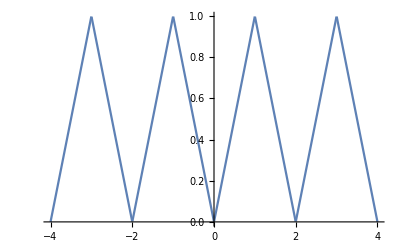

```mathematica
g[x_]:=If[EvenQ[Floor[x]],Abs[x-Floor[x]],Abs[FractionalPart[Ceiling[x]-x]]];Plot[g[x],{x,-4,4}]
```

Let f(x)=∑_(k=0)^∞ (3/4)^k g(4^k x).  It turns out that f is continuous everywhere but differentiable nowhere!

```mathematica
f[x_,n_]:=∑_(k=0)^n (3/4)^k*g[4^k*x]
```

```mathematica
Manipulate[Plot[f[x,n],{x,0,1},PlotRange->{0,3},PlotStyle->Thick,PerformanceGoal->"Quality"],{n,0,5,1}]
```

```mathematica
Manipulate[Show[Plot[f[x,10],{x,a-b,a+b},PlotRange->{0,3},PlotPoints->30],ListPlot[{{a,f[a,10]}},PlotStyle->{Red,PointSize[.03]}]],{a,0,1},{b,1,.01,-.01}]
```

```mathematica
Manipulate[Show[Plot[f[x,10],{x,a-b,a+b},PlotRange->{f[a,10]-2*Abs[f[a-b,10]-f[a+b,10]],f[a,10]+2*Abs[f[a-b,10]-f[a+b,10]]}],ListPlot[{{a,f[a,10]}},PlotStyle->{Red,PointSize[.03]}]],{a,0,1},{b,1,.01,-.01}]
```

### A function which is differentiable everywhere need not have a derivative which is everywhere continuous

Let f(x)=x^2 sin(1/x) if x≠0 and f(0)=0.

```mathematica
f[x_]:=If[x≠0,x^2*Sin[1/x],0];Manipulate[Plot[{f[x],f'[x]},{x,-a,a},PlotRange->{-1.1,1.4},PlotStyle->{{Thick,Blue},{Thick,Red}},PerformanceGoal->"Quality"],{a,1,.001,-.001}]
```

```mathematica
Limit[(f[a]-f[0])/(a-0),a->0]
```

```mathematica
g[x_]:=x^2*Sin[1/x];g'[0]
```

### A function which is differentiable everywhere need not have a derivative which is bounded

Let f(x)=x^2 sin(1/x^2) if x≠0 and f(0)=0.

```mathematica
f[x_]:=If[x≠0,x^2*Sin[1/x^2],0]
```

```mathematica
Limit[(f[a]-f[0])/(a-0),a->0]
```

```mathematica
Plot[{f[x],f'[x]},{x,-1,1}]
```

## Another Counter-Intuitive Example

### A Simple-Looking Recusively Defined Sequence

Define a sequence x_0,x_1,x_2,x_3,… by letting x_0=.1 and letting x_n=4 x_(n-1)-4 x_(n-1)^2 for integers n≥1.  What is the behavior of this sequence as n gets larger and larger?

```mathematica
f[x_]:=4x-4x^2;
```

```mathematica
NestList[f,.1,50]
```

{0.1,0.36,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961563,0.147837,0.503924,0.999938,0.000246305,0.000984976,0.00393603,0.0156821,0.0617448,0.23173,0.712124,0.820014,0.590364,0.967337,0.126384,0.441645,0.986379,0.053742,0.203415,0.64815,0.912207,0.320342,0.870893,0.449754,0.989902,0.0399861,0.153549,0.519886,0.998418,0.00631737,0.0251098,0.0979173,0.353318,0.913938,0.314623,0.862541,0.474255,0.997349,0.0105765,0.0418584,0.160425,0.538755}

```mathematica
Manipulate[ListPlot[Transpose[{NestList[f,.1,b],Table[0,{k,0,b}]}],PlotStyle->{Red,PointSize[.02]},PlotRange->{{0,1},{-1,1}},Ticks->{{0,.2,.4,.6,.8,1}, },Axes->{True,False}],{b,0,50,1}]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],Joined->True],ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],PlotStyle->{Red,PointSize[.025]}],PlotRange->{{0,50},{0,1}},AxesLabel->{"n","x_n"}],{b,0,50,1}]
```

This is an example of "chaos".  Certain statistical/probabilistic patterns are evident, however.

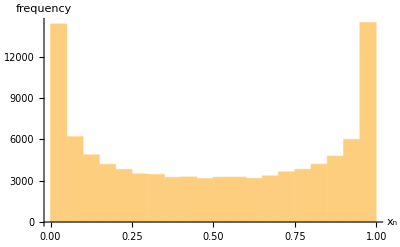

```mathematica
Histogram[NestList[f,.1,100000],AxesLabel->{"x_n","frequency"}]
```

An area of math called Ergodic theory is where the probabilistic patterns in these deterministic situations is studied.

## A Fundamental Result in Calculus: The Mean Value Theorem ("MVT! MVT! MVT!") (Note: you'll want to come back to this section of this notebook often in the next couple months)

### Statement of the MVT: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b), then there exists a number c ∈ (a,b) such that f^′(c)=(f(b) - f(a))/(b - a)

### illustrating the theorem:

For the function f(x)=x^2 over an interval [a,b].

```mathematica
f[x_]:=x^2;Manipulate[Show[Plot[{f[x],((f[b]-f[a])/(b-a))*(x-a)+f[a],f'[(a+b)/2]*(x-(a+b)/2)+f[(a+b)/2]},{x,-4,4},PlotRange->{-5,15},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}}],ListPlot[{{a,f[a]},{b,f[b]},{(a+b)/2,f[(a+b)/2]},{a,0},{b,0},{(a+b)/2,0}},PlotStyle->PointSize[.02]],AxesLabel->{"x","y"}],{a,-3,b-.01},{b,-2.9,3}]
```

For an "arbitrary" differentiable function f over an interval [a,b] (the following code does not work perfectly because FindRoot is not guaranteed to find a c between a and b (it might find a c outside this interval), though it probably will for most examples):

```mathematica
f[x_]:=Cos[2x]-3x;Manipulate[sol=FindRoot[f'[c]==(f[b]-f[a])/(b-a),{c,(a+b)/2}];Show[Plot[{f[x],((f[b]-f[a])/(b-a))*(x-a)+f[a],f'[c/.sol]*(x-c/.sol)+f[c/.sol]},{x,-4,4},PlotRange->{-10,10},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}}],ListPlot[{{a,f[a]},{b,f[b]},{c/.sol,f[c/.sol]},{a,0},{b,0},{c/.sol,0}},PlotStyle->PointSize[.02]],AxesLabel->{"x","y"}],{a,-3,b-.01},{b,-2.9,3}]
```

### Important consequences ("corollaries") of the theorem:

#### The Increasing Function Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f^′(x)>0 for all x in the open interval (a,b), then f is a strictly increasing function on the closed interval [a,b]. (Note: there is a "Decreasing Function Theorem" too).

```mathematica
Manipulate[Plot[x^3,{x,-a,a},PlotRange->{-a,a},PlotStyle->{Thick,Red}],{a,3,.0001}]
```

Warning:  you need to be careful in how you interpret this theorem.  Somewhat counter-intuitively, just because f^′(c)>0 at some number c, that does not mean that f is increasing for all x near c.  Consider the example below.

#### Example for Warning above

```mathematica
f[x_]:=If[x≠0,x/2+x^2*Sin[1/x],0]
```

```mathematica
Limit[(f[a]-f[0])/(a-0),a->0]
```

```mathematica
Manipulate[Plot[f[x],{x,-a,a},PlotRange->{-2a,2a},AxesLabel->{"x","y"},PlotStyle->Thick],{a,1,.01,-.01}]
```

```mathematica
Manipulate[Plot[f[x],{x,-a,a},PlotRange->{-a/20,a/20},AxesLabel->{"x","y"},PlotStyle->Thick],{a,1,.5,-.01}]
```

```mathematica
Manipulate[Show[Plot[f[x],{x,-a+.01,a+.01},PlotRange->{-a+f[.01],a+f[.01]},AxesLabel->{"x","y"},PlotStyle->Thick],ListPlot[{{.01,f[.01]}},PlotStyle->{PointSize[.02],Black}]],{a,1,.0001,-.0001}]
```

```mathematica
f'[.01]
```

```mathematica
Plot[f'[x],{x,-1,1},AxesLabel->{"x","y"}]
```

#### The Constant Function Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f^′(x)=0 for all x in the open interval (a,b), then f is a constant on the closed interval [a,b].

#### Antiderivatives of the same function differ by constants: Let f and g be two functions which are continuous on the closed interval [a,b] and differentiable on the open interval (a,b). If f^′(x)=g^′(x) for all x in the open interval (a,b), then there is a constant C such that f(x)=g(x)+C for all x in the closed interval [a,b].

#### Other applications: (1) the first derivative test, (2) y=a ⅇ^(b x) is the "general solution" of the differential equation y^′=b y. Also, this function is the unique solution of the "initial value problem" y^′=b y, y(0)=a. (3) y=a cos(k x)+b sin(k x) is the "general solution" of the differential equation y^″=-k^2y. Also, this function is the unique solution of the initial value problem y^″=-k^2y, y(0)=a, y'(0) = b k. (4) The Fundamental Theorem of Calculus. And the list goes on and on and on...

### Idea of Proof of the Theorem (if we "Work Backwards"):

#### It can be derived from Rolle's Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f(a)=f(b), then there exists a number c ∈ (a,b) such that f^′(c)=0.

The MVT for a given function f and given interval [a,b] follows by applying Rolle's Theorem to the function g(x)=f(x)-L(x), where L(x)=(f(b)-f(a))/(b-a)(x-a)+f(a) is the function whose graph is the secant line to the graph of f between the points (a,f(a)) and (b,f(b)).

#### ...which can be derived from Fermat's Theorem (not to be confused with Fermat's Last Theorem or Fermat's Little Theorem): If c is a local extreme point (a local max or a local min) of a function f over an open interval (a,b), then either f is not differentiable at c or f^′(c)=0.

For a given function f and a given interval [a,b], Rolle's theorem follows from Fermat's theorem because of the following:

#### The Extreme Value Theorem (EVT): If f is a continuous function on the closed interval [a,b], then f has a global maximum and global minimum value on this interval. That is, in this situation there exist numbers c and d in the closed interval [a,b] such that f(c)≤f(x)≤f(d) for all x∈[a,b].

The truth of Fermat's Theorem follows from the definition of the derivative (which is based on the limit concept) and the definition of a local extreme point.  The truth of the EVT depends on a number of foundational ideas for our course.  They are:

#### The Definition of Continuity: A function f defined on an interval containing a number c is said to be continuous at c if for all ϵ>0, there exists a number δ>0 such that |f(x)-f(c)|<ϵ for all x in the interval which satisfy the condition that 0<|x-c|<ϵ. A function f is said to be continuous on an interval if it is continuous at every point in that interval. In effect, continuity at a number c says that lim_(x→c) f(x)=f(c) (assuming x is close enough to c to be in the domain of f ). In other words, the definition of continuity is inextricably linked to the concept of limits.

#### The Definition of Convergence of a Sequence: A sequence {x_n} is said to converge to a number L if for all ϵ>0, there exists a positive integer N such that |x_n-L|<ϵ for all positive integers n satisfying the condition that n≥N.

#### The Definition of a Bounded Sequence: A sequence {x_n} is bounded if there exists a number M>0 such that |x_n|<M for all positive integers n.

#### The Definition of a Subsequence of a Given Sequence: A subsequence of a given sequence {x_n} is a sequence made up of some of the terms of {x_n} in the same order they appear in the original sequence. To be more precise, a subsequence of {x_n} is any sequence that takes the form {x_p_n}, where {p_n} is a strictly increasing sequence of positive integers.

#### The (simplest form of the) Bolzano-Weierstrass Theorem: Every bounded sequence of real numbers has a convergent subsequence. Moreover, if {x_n} is a sequence of real numbers from the closed interval [a,b], then {x_n} has a subsequence {x_p_n} that converges to a real number in [a,b].

All of these things, in turn, are dependent on the Completeness Axiom (also called the Least Upper Bound Property).  This property is the most important property that distinguishes the field of real numbers ℝ from the field of rational numbers ℚ.

#### Completeness Axiom: For every nonempty set of real numbers which is bounded above, there exists a real number which is the least upper bound for that set. (that is, there is a smallest upper bound for the set).

Every nonempty set of rational numbers which is bounded above also has a least upper bound (since every rational number is a real number).  However, this least upper bound need not be a rational number!  In all likelihood, the least upper bound of a randomly chosen bounded set of rational numbers will be an irrational number (more on this when we get to section 1.4 of the textbook).

## Fields

The definition of a field is given in the text on page 6.  You know (from your algebraic structures days) that a field can be described more succinctly as a commutative ring with unity in which every nonzero element is a unit...right?  Alternatively, you could also say a field is an Abelian group under addition whose nonzero elements form an Abelian group under multiplication such that the distributive property of multiplication over addition also holds (which is a condition for every ring).

While all of this sounds real fancy, you should take it to mean that fields are essentially "as nice as it gets" in algebra.  Every ordinary kind of property that you would hope would be true, is true.

The rationals ℚ, the reals ℝ, and the complex numbers ℂ are the most commonly used fields, but you will recall from algebraic structures that there are infinitely many others, including things like ℚ(√2)={a+b √2| a,b∈ℚ} and ℚ(2^(1/3))={a+b 2^(1/3)+(c(2^(1/3)))^2| a,b,c∈ℚ} and also fields.

You may be either happy or sad to know that in Real Analysis, we only concern ourselves with ℚ and ℝ (and mostly just with ℝ).

## Ordered Sets

The book gives an intuitive definition of an order < on a set S on page 7, making S an ordered set.  In a nutshell, you want all pairs of distinct elements of S to be ordered in some way with respect to each other (trichotomy) and you want the ordering to satisfy the transitive property.

Here, for your interest, I give the precice definition of an order on a set and an ordered set (based on the concept of a relation).  I also give the definition of a partial order on a set and a partially ordered set.  This material is not necessary for our course, but if you are interested you can pursue it.

Given a nonempty set S, any nonempty subset R⊆S×S={(a,b) | a,b∈S} is called a relation on S.  A (strict, total) order R on S is a relation with the properties:  (1) (a,a)∉R for all a∈S, (2) if a,b∈S with a≠b, then either (a,b)∈R or (b,a)∈R but not both (saying (a,b)∈R means a<b) and (3) if (a,b)∈R and (b,c)∈R, then (a,c)∈R.  We call S with a given order R an ordered set...and we sometimes write it as the pair (S,R).  Essentially, ordered sets can be modeled as "number lines".  Also, the "ordinary" less than symbol <  on ℝ can be modeled, as a relation, as a "diagonal half-plane" R={(x,y) | x<y} when we think of it as a subset of ℝ^2=ℝ×ℝ.

```mathematica
RegionPlot[x<y,{x,-3,3},{y,-3,3},BoundaryStyle->Directive[Dashed]]
```

In the above picture, you should think of the dashed line along y=x as not part of the set R.  The dashed lines along the left side and top should be part of the set R (as should all points going off to infinity above the line y=x).

A (strict) partial order R on S is a relation that satisfies:  (1) (a,a)∉R for all a∈S and (2) if (a,b)∈R and (b,c)∈R, then (a,c)∈R.  A set S with a partial order defined on it is called a partially ordered set, or poset for short.  Note the key difference with a total order that distinct elements need not be related for partial orders.  Any directed graph (or “digraph”, for short) from Discrete Mathematics is an example of a partially ordered set.  In particular, trees are partially ordered sets.  It is interesting that every expression in Mathematica can be represented as a (hierarchical) tree.

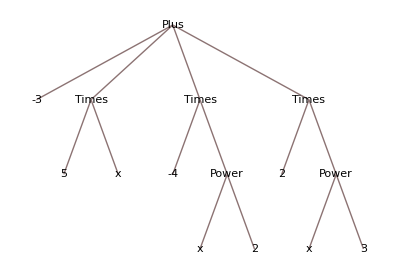

```mathematica
TreeForm[2x^3-4x^2+5x-3]
```

## Ordered Fields

In the notation of the preceding section, an ordered field is a field F on which a strict total order R has been defined which also satisfies the following properties:  (1) (0,x),(0,y)∈R⟹(0,x+y)∈R, (2) (0,x),(0,y)∈R⟹(0,x y)∈R, and (3) (x,y)∈R⟺(0,y-x)∈R (compare these to the book's statements on page 8).

## Prove: if x<y and z>0, then x z<y z.

## Why are the Rational Numbers "Defective" for Calculus?

The reason for this has already been described a little bit at the end of the preceding section of this notebook.  The rational numbers do not satisfy the Completeness property.  There exist nonempty bounded sets of rational numbers which have no least upper bound in the field of rational numbers (and also perhaps no greatest lower bound in the field of rational numbers either).  This failure of completeness of the field of rational numbers means there exist sequences of rational numbers which do not converge to a rational number.  

You actually probably knew this fact before you took this course, but stated in a different way.  In particular, you probably knew that the decimal expansions of irrational numbers, such as π and ⅇ and √2, have no repeating pattern.

This does not rule out the existence of certain kinds of patterns.  It only rules out the presense of (infinitely) repeating patterns.

The following will display the frequency of the various digits.  Are there patterns?  Probably nothing definitive.

```mathematica
Manipulate[Histogram[Drop[Flatten[RealDigits[N[π,n]]],-1]],{n,1,1000,1},LabelStyle->Large]
```

```mathematica
Manipulate[Histogram[Drop[Flatten[RealDigits[N[ⅇ,n]]],-1]],{n,1,10000,1},LabelStyle->Large]
```

```mathematica
Manipulate[Histogram[Drop[Flatten[RealDigits[N[√2,n]]],-1]],{n,1,10000,1},LabelStyle->Large]
```

Since, for example, the number ⅇ is very important in Calculus, that gives one reason why the rational numbers are "defective" for Calculus.  More fundamentally, if we just use rational numbers, we cannot be sure that the limit of a sequence of numbers will be a rational number.  For example, the following sequence of rational numbers (we see just the start of it on Mathematica), converges to π, which we know is irrational.

```mathematica
Table[N[π,n],{n,1,50}]
```

## What are Irrational Numbers anyway? Do they really exist?

The early ancient Greeks (in particular, the Pythagorean school) had fundamental assumptions about nature and its measurement.  In particular, they assumed all lengths were commensurable.  The upshot of this is that they thought that the ratio of any two lengths would be a rational number (originally they didn't even imagine the existence of rational numbers).  The Pythagorean Theorem, which they also held dear, changed all of this.  Once they realized that the length √2 of the diagonal of a square of side length one was not rational, they eventually decided that they preferred the heresy of the existence of irrational numbers rather than give up their beautiful and beloved Pythagorean Theorem (though, so the story goes, Hippasus had to be sacrificed at sea because of the heresy).

But some people still have philosophical issues with irrational numbers.  After all, if you don't (and cannot) know every digit of a number like π, can you really "know" the number?  Can you even be sure it exists?

We don't want to get into mathematical philosophy too much here, but it is of interest to a lot of people.  Basically, we will view the entire real number system "axiomatically" or "synthetically", where we just focus on using all the properties that we have always "known" from 8th grade or so on up, in addition to the Completeness property referred to earlier in this notebook.  If you are interested though, you can mathematically construct the real numbers from the rational numbers via either "Dedekind cuts“or equivalence classes of "Cauchy sequences" of rational numbers.

By the way, even though all the digits of π cannot be known by any finite being (human or machine), we can, in principle, "find" any digit we want.  For example, the 1,000,000th (millionth) digit (when the digit in the ones spot, "3", is included) is a "5".

```mathematica
Last[Drop[Flatten[RealDigits[N[π,1000000]]],-1]]
```

## Measuring "Length" or "Size": Absolute Value and its Properties (especially the Triangle Inequality) and Norms

### Basic Properties (Theorem 1.4 on page 10)

### Triangle Inequality (Theorem 1.5 on page 10)

#### Graphical illustration

```mathematica
AxesPlot=ParametricPlot3D[{{t,0,0},{0,t,0},{0,0,t}},{t,-6,6},PlotStyle->Thick];Show[Plot3D[{Abs[x+y],Abs[x]+Abs[y]},{x,-3,3},{y,-3,3},AxesLabel->{"x","y","z"},PlotStyle->{Red,Blue}],AxesPlot]
```

### Reverse Triangle Inequality (Theorem 1.6 on page 11)

#### Graphical illustration

```mathematica
AxesPlot=ParametricPlot3D[{{t,0,0},{0,t,0},{0,0,t}},{t,-6,6},PlotStyle->Thick];Show[Plot3D[{Abs[Abs[x]-Abs[y]],Abs[x-y]},{x,-3,3},{y,-3,3},AxesLabel->{"x","y","z"},PlotStyle->{Red,Blue}],AxesPlot]
```

### Extensions: Norms

There are many other ways of measuring length or size of a mathematical object.  The abstract concept that encompasses these many ways is the concept of a norm.  Norms are real-valued functions defined on vector spaces that satisfy certain intuitive properties.  Norms are usually denoted by absolute-value (or "double" absolute-value) type symbols.  That is, either by |·| or ‖·‖, where the dot · just represents the fact that "something must go here".

If V is a vector space over the field of real numbers ℝ, then we want the following properties to hold for norms (because they are the most fundamental properties that norms "should" have):  (1) ‖v‖≥0 for all v∈V, (2) ‖v‖=0 iff v = 0, (3) ‖a v‖=|a|‖v‖ for all a∈ℝ and for all v∈V, and (4) ‖u+v‖≤‖u‖+‖v‖ for all u,v∈V (the triangle inequality).

There are many important examples of norms:

If x=(x_1,x_2,x_3,…,x_n)∈ℝ^n and p≥1 is a real number, then (‖x‖)_p=(∑_(i=1)^n x_i^p)^(1/p) satisfies all the properties of a norm and is called the p-norm (when p = 2, we get the "ordinary" Euclidean norm).  Another norm on ℝ^n is called the maximum norm.  It is defined by the equation  (‖x‖)_∞=max_i |x_i|.

Given an n×n matrix A (in the vector space of all such matrices...where "vector" addition is matrix addition...the "vectors" are matrices), an important kind of matrix norm is the operator norm ‖A‖=max_(‖x‖≤1) ‖A x‖, where ‖x‖ and ‖A x‖ represent the ordinary Euclidean norms of x and A x, respectively.

Which norm should you use?  For our course, we won't have to worry about this.  But in general, the norm you use depends on which one is easiest to work with in various circumstances, not necessarily which one gives you some preconceived notion of what the "true" length or size of a vector is.  In many situations, it actually doesn't matter which one you use, because in many situations, different norms on the same space are equivalent.

## The Triangle Inequality

## Extensions: Algebraic and Transcendental Numbers

The set of (real) algebraic numbers can be defined as those real numbers which are roots to some nonzero polynomial with integer coefficients.  Those real numbers which are not algebraic are called transcendental (real numbers).  The easiest way to prove the existence of transcendental numbers is to prove that the set of algebraic numbers is countable, whereas the set of all real numbers is uncountable.  It is harder to prove that particular numbers are transcendental.  However two of our favorite numbers, ⅇ and π, can be shown to be transcendental by the Lindemann-Weierstrass Theorem.

## Extensions: Weird Formulas Involving π

There are hundreds and perhaps thousands of weird formulas out there that mysteriously involve the number π, for seemingly no apparent "deep" reason.  Evaluate the following cells to see some.

Some sums generated by Euler:

```mathematica
∑_(k=1)^∞ 1/k^2
```

π^2/6

```mathematica
∑_(k=1)^∞ 1/k^4
```

π^4/90

```mathematica
∑_(k=1)^∞ 1/k^6
```

π^6/945

```mathematica
Table[∑_(k=1)^∞ 1/k^(2s),{s,1,10}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555,(691 π^12)/638512875,(2 π^14)/18243225,(3617 π^16)/325641566250,(43867 π^18)/38979295480125,(174611 π^20)/1531329465290625}

Oddly enough, nobody knows the exact values of these types of sums when the power of each denominator is odd...so they give it a cool sounding name...like “zeta” (and can, of course, approximate them)...the Riemann Zeta Function is actually one of the most important functions in all of mathematics...it’s related to the most important unsolved problem in math...the Riemann hypothesis

```mathematica
∑_(k=1)^∞ 1/k^3
```

Zeta[3]

```mathematica
N[%,100]
```

```mathematica
∑_(k=1)^∞ 1/k^5
```

```mathematica
N[%,100]
```

A sum used by Fourier and others:

```mathematica
∑_(k=1)^∞ (-1)^(k-1)/(2k-1)
```

An expression related to the Normal distribution:

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

The Wallis product:

```mathematica
∏_(k=1)^∞ (4k^2)/(4k^2-1)
```

Here are a couple that actually involve some trigonometry!  (So are these mysterious or not?)

```mathematica
∫_(-∞)^∞ Sin[x]/x ⅆx
```

```mathematica
N[{16ArcTan[1/5]-4ArcTan[1/239],π},100]
```

This last one comes from Machin.